```mathematica
Quit[]
```

## Input

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts-3.11/FeynArts.m"
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

```mathematica
<<"/home/riccardo/Documents/Tesi/ABISS/ABISS.m"
```

+++++ ABISS` +++++
Version 1.0.0

Amplitudes Builder, Interference Solver and Simplifier

First::nofirst: {} has zero length and no first element.

StringJoin::string: String expected at position 1 in First[{}]<>/Models.

First::nofirst: Alternatives[] has zero length and no first element.

StringJoin::string: String expected at position 1 in First[Alternatives[]]<>/Models.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[\b\B].

First::nofirst: Alternatives[] has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[\b\B].

General::stop: Further output of First::normal will be suppressed during this calculation.

Set the path of the Folder where to save final results and temporary results:

```mathematica
SetPath[NotebookDirectory[]];
```

Define the process:

```mathematica
SetProcess[{F[3,{1,o}],-F[4,{1,o}]}->{F[1,{2}],-F[2,{2}]}];
```

Generate default Input files

```mathematica
GenerateInput[];
```

Input file /home/riccardo/Documents/Tesi/TestABISS/ExampleProcess/input/kinematics.m already exist. It will NOT be overwritten.

Input file /home/riccardo/Documents/Tesi/TestABISS/ExampleProcess/input/integral_families.m already exist. It will NOT be overwritten.

Import the input files (kinematics + integral families).

```mathematica
ImportInput[];
```

Imported input file /home/riccardo/Documents/Tesi/TestABISS/ExampleProcess/input/integral_families.m.

Imported input file /home/riccardo/Documents/Tesi/TestABISS/ExampleProcess/input/kinematics.m.

## Diagrams generation

Generate diagrams using feynarts (charged current drell-yan, one loop boxes and born).

```mathematica
SetOptions[InsertFields,  Model -> "/home/riccardo/Documents/Tesi/ABISS/models/SMbgf_Anglerfish", GenericModel ->"Lorentzbgf", InsertionLevel->{Particles}, Restrictions->{NoQuarkMixing,NoLightFHCoupling}, ExcludeParticles-> {}];
```

```mathematica
process={F[3,{1,o}],-F[4,{1,o}]}->{F[1,{2}],-F[2,{2}]};
```

```mathematica
topologiesBorn=CreateTopologies[0,2-> 2];
```

```mathematica
fieldsBorn=InsertFields[topologiesBorn, process];
```

loading generic model file /home/riccardo/Programs/FeynArts/FeynArts-3.11/Models/Lorentzbgf.gen

> $GenericMixing is OFF

generic model {Lorentzbgf} initialized

loading classes model file /home/riccardo/Documents/Tesi/ABISS/models/SMbgf_Anglerfish.mod

> 60 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 689 vertices

> 334 counterterms of order 1

> 2 counterterms of order 2

classes model {/home/riccardo/Documents/Tesi/ABISS/models/SMbgf_Anglerfish} initialized

Excluding 48 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 1 Particles insertion

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 48 field point(s)

in total: 1 Particles insertion

```mathematica
topologies1L=CreateTopologies[1,2-> 2,BoxesOnly];
```

```mathematica
fields1L=InsertFields[topologies1L, process];
```

Excluding 48 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 3 Particles insertions

> Top. 8: 3 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

Restoring 48 field point(s)

in total: 6 Particles insertions

```mathematica
amp1L=CreateFeynAmp[fields1L];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 3 Particles amplitudes

> Top. 2: 3 Particles amplitudes

in total: 6 Particles amplitudes

```mathematica
ampBorn=CreateFeynAmp[fieldsBorn];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

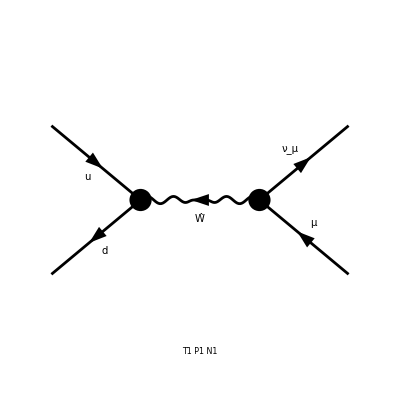

```mathematica
Paint[fieldsBorn];
```

> Top. 1 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 2 aebf/cgdh/efehfggh.m, 0 diagrams

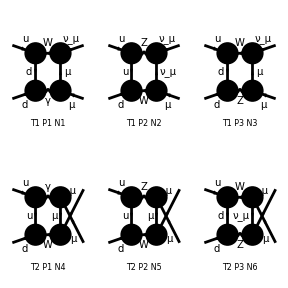

```mathematica
Paint[fields1L];
```

Extract amplitudes in a Abiss-friendly format, then save them. Put desired masses to zero by hand.

```mathematica
massesToZero={MD-> 0,MM->0, MU-> 0};(*Mathematica Replace All*)
```

```mathematica
myAmp1L=ExtractAmplitude[amp1L]/.massesToZero;
myAmpBorn=ExtractAmplitude[ampBorn]/.massesToZero;
```

```mathematica
SaveAmplitudes[myAmp1L,"OneLoopAmplitudes.m"];
SaveAmplitudes[myAmpBorn,"BornAmplitudes.m"];
```

Amplitudes saved in /home/riccardo/Documents/Tesi/TestABISS/ExampleProcess/feynArts_amplitudes/OneLoopAmplitudes.m

Amplitudes saved in /home/riccardo/Documents/Tesi/TestABISS/ExampleProcess/feynArts_amplitudes/BornAmplitudes.m

## Interference

### 0th Perturbative Order

```mathematica
test0=AmpSquare[myAmpBorn[[1]],myAmpBorn[[1]]];
Simplify[test0]
```

(EL^4 gWdu^2 gWNl^2 (-(-4+d) s12^2+(4-5 d+d^2) s13^2-(8-5 d+d^2) s23^2) CKM[1,1] CKM[1,1]^*)/((MW^2-s12)^2)

### 1st Perturbative Order

Compute a single interference term “by hand”:

```mathematica
test=AmpSquare[myAmp1L[[1]],myAmpBorn[[1]]];
Simplify[test]
```

1/(16 π^4 (MW^2-s12))ⅈ EL^6 gAd gAl gWdu^2 gWNl^2 CKM[1,1] CKM[1,1]^* KiraPropagator[q1,0] KiraPropagator[p2+q1,0] KiraPropagator[p2-p4+q1,0] KiraPropagator[p2-p3-p4+q1,MW] (-80 s12 s13 SP[p3,q1]+60 d s12 s13 SP[p3,q1]-14 d^2 s12 s13 SP[p3,q1]+d^3 s12 s13 SP[p3,q1]+40 s13 s23 SP[p3,q1]-24 d s13 s23 SP[p3,q1]+4 d^2 s13 s23 SP[p3,q1]+16 s12^2 SP[p4,q1]-12 d s12^2 SP[p4,q1]+2 d^2 s12^2 SP[p4,q1]-16 s13^2 SP[p4,q1]+20 d s13^2 SP[p4,q1]-4 d^2 s13^2 SP[p4,q1]+16 s12 s23 SP[p4,q1]+4 d s12 s23 SP[p4,q1]-6 d^2 s12 s23 SP[p4,q1]+d^3 s12 s23 SP[p4,q1]-8 s23^2 SP[p4,q1]+4 d s23^2 SP[p4,q1]+208 s12 SP[p3,q1] SP[p4,q1]-176 d s12 SP[p3,q1] SP[p4,q1]+48 d^2 s12 SP[p3,q1] SP[p4,q1]-4 d^3 s12 SP[p3,q1] SP[p4,q1]+SP[p2,q1] (-16 s12^2+12 d s12^2-2 d^2 s12^2-32 s13^2+24 d s13^2-8 d^2 s13^2+d^3 s13^2+8 s12 s23-8 d s12 s23+2 d^2 s12 s23+32 s23^2-8 d s23^2-4 d^2 s23^2+d^3 s23^2-2 (-112+76 d-16 d^2+d^3) s23 SP[p3,q1]-2 (8+12 d-8 d^2+d^3) s13 SP[p4,q1])+2 SP[p1,q1] (-2 (-52+44 d-12 d^2+d^3) s12 SP[p2,q1]-(8+12 d-8 d^2+d^3) s13 SP[p3,q1]+(-4+d) ((-4+d) s13 (s12+(-2+d) s23)-(28-12 d+d^2) s23 SP[p4,q1]))-68 s12^2 SP[q1,q1]+56 d s12^2 SP[q1,q1]-14 d^2 s12^2 SP[q1,q1]+d^3 s12^2 SP[q1,q1]-12 s13^2 SP[q1,q1]-4 d s13^2 SP[q1,q1]+2 d^2 s13^2 SP[q1,q1]+76 s23^2 SP[q1,q1]-44 d s23^2 SP[q1,q1]+6 d^2 s23^2 SP[q1,q1])

Compute all interference term automatically (in this case, also simplifying). Files are saved as Contribution_i_j.m. An optional argument modifies the file name.

```mathematica
SquareSimplifyAndSave[myAmp1L,myAmpBorn]
```

Computed contribution 1-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/ExampleProcess//interferences/Contribution_1_1.m.

Computed contribution 2-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/ExampleProcess//interferences/Contribution_2_1.m.

Computed contribution 3-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/ExampleProcess//interferences/Contribution_3_1.m.

Computed contribution 4-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/ExampleProcess//interferences/Contribution_4_1.m.

Computed contribution 5-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/ExampleProcess//interferences/Contribution_5_1.m.

Computed contribution 6-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/ExampleProcess//interferences/Contribution_6_1.m.

## Shift

Perform the shift to one of the integral families in the input file. Please use the following input file for this test:

userLoopMomenta={
q1
};
(* User-defined integral families *)
userIntegralFamiliesNames={
TopoCM,
TopoCMp,
TopoC2M,
TopoC2Mp
};
userPropagatorMomenta[TopoCM]={
	q1,
	-p1+q1,
	p2+q1,
	p3-p1+q1
};
userIntegralMasses[TopoCM]={0,M1,0,0};
userPropagatorMomenta[TopoCMp]={
	q1,
	-p1+q1,
	p2+q1,
	-p3+p2+q1
};

userIntegralMasses[TopoCMp]={0,0,M1,0};

userPropagatorMomenta[TopoC2M]={
	q1,
	-p1+q1,
	p2+q1,
	p3-p1+q1
};

userIntegralMasses[TopoC2M]={0,M1,M2,0};

userPropagatorMomenta[TopoC2Mp]={
	q1,
	-p1+q1,
	p2+q1,
	-p3+p2+q1
};

userIntegralMasses[TopoC2Mp]={0,M1,M2,0};

The shift can be done by hand.
Use ExtractFamily to check if an expression is already recognised as one of the integral families. Our test is already written in terms of an integral family:

```mathematica
ExtractFamily[test]
```

{TopoCM,{MW}}

Now let us define an expression which cannot be immediately recognised:

```mathematica
test2=test/.{q1-> q1+p3};
ExtractFamily[test2]
```

{False}

The shift to write it in terms of integral families can be obtained with ShiftToIntegralFamily:

```mathematica
ShiftToIntegralFamily[test2]
ExtractFamily[test2/.%]
```

{q1→-p3+q1}

{TopoCM,{MW}}

The shift can also be done automatically with ShiftAndSave. The flag indicates if to overwrite (True) or not (False, generates another folder with the result before the shift) the result. Files are saved as Contribution_i_j.m. An optional argument modifies the file name.

```mathematica
Do[
ShiftAndSave[i,j,False];
,{i,6},{j,1}]
```

Integral family {TopoCM, {MW}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/ExampleProcess/interferences/Contribution_1_1.m.

Integral family {TopoC2M, {MZ, MW}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/ExampleProcess/interferences/Contribution_2_1.m.

Integral family {TopoC2M, {MW, MZ}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/ExampleProcess/interferences/Contribution_3_1.m.

Integral family {TopoCMp, {MW}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/ExampleProcess/interferences/Contribution_4_1.m.

Integral family {TopoC2Mp, {MZ, MW}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/ExampleProcess/interferences/Contribution_5_1.m.

Integral family {TopoC2Mp, {MW, MZ}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/ExampleProcess/interferences/Contribution_6_1.m.

## KiraInput

Can be done by hand on a single term:

```mathematica
test3=GenerateKiraInput[test]
```

1/(16 π^4 (MW^2-s12))ⅈ (-52+44 d-12 d^2+d^3) EL^6 gAd gAl gWdu^2 gWNl^2 s12 CKM[1,1] CKM[1,1]^* userIntegral[TopoCM,{MW},-1,1,1,1]-1/(32 π^4 (MW^2-s12))ⅈ EL^6 gAd gAl gWdu^2 gWNl^2 (2 (-52+44 d-12 d^2+d^3) s12-(8+12 d-8 d^2+d^3) s13+(-112+76 d-16 d^2+d^3) s23) CKM[1,1] CKM[1,1]^* userIntegral[TopoCM,{MW},0,0,1,1]-1/(32 π^4 (MW^2-s12))ⅈ EL^6 gAd gAl gWdu^2 gWNl^2 (2 (-52+44 d-12 d^2+d^3) s12-(8+12 d-8 d^2+d^3) s13+(-112+76 d-16 d^2+d^3) s23) CKM[1,1] CKM[1,1]^* userIntegral[TopoCM,{MW},0,1,0,1]-1/(16 π^4 (MW^2-s12))ⅈ EL^6 gAd gAl gWdu^2 gWNl^2 ((8+12 d-8 d^2+d^3) s13-(-112+76 d-16 d^2+d^3) s23) CKM[1,1] CKM[1,1]^* userIntegral[TopoCM,{MW},0,1,1,0]-1/(32 π^4 (MW^2-s12))ⅈ EL^6 gAd gAl gWdu^2 gWNl^2 (-2 (-60+50 d-13 d^2+d^3) s12^2-24 s13^2+8 d s13^2+4 d^2 s13^2-d^3 s13^2-160 s13 s23+88 d s13 s23-12 d^2 s13 s23-120 s23^2+80 d s23^2-16 d^2 s23^2+d^3 s23^2-2 s12 ((-4+d)^2 s13-(-2+d)^2 s23)+MW^2 (2 (-52+44 d-12 d^2+d^3) s12-(8+12 d-8 d^2+d^3) s13+(-112+76 d-16 d^2+d^3) s23)) CKM[1,1] CKM[1,1]^* userIntegral[TopoCM,{MW},0,1,1,1]-1/(32 π^4 (MW^2-s12))ⅈ (8+12 d-8 d^2+d^3) EL^6 gAd gAl gWdu^2 gWNl^2 s13 CKM[1,1] CKM[1,1]^* userIntegral[TopoCM,{MW},1,-1,1,1]+1/(16 π^4 (MW^2-s12))ⅈ EL^6 gAd gAl gWdu^2 gWNl^2 (2 (-52+44 d-12 d^2+d^3) s12+(-112+76 d-16 d^2+d^3) s23) CKM[1,1] CKM[1,1]^* userIntegral[TopoCM,{MW},1,0,0,1]-1/(32 π^4 (MW^2-s12))ⅈ EL^6 gAd gAl gWdu^2 gWNl^2 (2 (-52+44 d-12 d^2+d^3) s12-(8+12 d-8 d^2+d^3) s13+(-112+76 d-16 d^2+d^3) s23) CKM[1,1] CKM[1,1]^* userIntegral[TopoCM,{MW},1,0,1,0]-1/(32 π^4 (MW^2-s12))ⅈ EL^6 gAd gAl gWdu^2 gWNl^2 s13 (2 (8+12 d-8 d^2+d^3) MW^2-(-56+44 d-12 d^2+d^3) s12+8 s13+12 d s13-8 d^2 s13+d^3 s13+88 s23-36 d s23+d^3 s23) CKM[1,1] CKM[1,1]^* userIntegral[TopoCM,{MW},1,0,1,1]-1/(32 π^4 (MW^2-s12))ⅈ (8+12 d-8 d^2+d^3) EL^6 gAd gAl gWdu^2 gWNl^2 s13 CKM[1,1] CKM[1,1]^* userIntegral[TopoCM,{MW},1,1,-1,1]-1/(32 π^4 (MW^2-s12))ⅈ EL^6 gAd gAl gWdu^2 gWNl^2 (2 (-52+44 d-12 d^2+d^3) s12-(8+12 d-8 d^2+d^3) s13+(-112+76 d-16 d^2+d^3) s23) CKM[1,1] CKM[1,1]^* userIntegral[TopoCM,{MW},1,1,0,0]+1/(32 π^4 (MW^2-s12))ⅈ EL^6 gAd gAl gWdu^2 gWNl^2 (2 (-52+44 d-12 d^2+d^3) s12 s13-56 s13^2+32 d s13^2-4 d^2 s13^2+(24-4 d-4 d^2+d^3) s12 s23-112 s13 s23+76 d s13 s23-16 d^2 s13 s23+d^3 s13 s23+24 s23^2-4 d s23^2-4 d^2 s23^2+d^3 s23^2+2 MW^2 (2 (-52+44 d-12 d^2+d^3) s12+(-112+76 d-16 d^2+d^3) s23)) CKM[1,1] CKM[1,1]^* userIntegral[TopoCM,{MW},1,1,0,1]+1/(16 π^4 (MW^2-s12))ⅈ (-52+44 d-12 d^2+d^3) EL^6 gAd gAl gWdu^2 gWNl^2 s12 CKM[1,1] CKM[1,1]^* userIntegral[TopoCM,{MW},1,1,1,-1]-1/(32 π^4 (MW^2-s12))ⅈ EL^6 gAd gAl gWdu^2 gWNl^2 (2 (8-6 d+d^2) s12^2+(-128+116 d-34 d^2+3 d^3) s12 s13-4 (4-5 d+d^2) s13^2+(16+4 d-6 d^2+d^3) s12 s23-4 (10-6 d+d^2) s13 s23+4 (-2+d) s23^2+MW^2 (2 (-52+44 d-12 d^2+d^3) s12-(8+12 d-8 d^2+d^3) s13+(-112+76 d-16 d^2+d^3) s23)) CKM[1,1] CKM[1,1]^* userIntegral[TopoCM,{MW},1,1,1,0]-1/(32 π^4 (MW^2-s12))ⅈ EL^6 gAd gAl gWdu^2 gWNl^2 s13 ((8+12 d-8 d^2+d^3) MW^4-2 (8-6 d+d^2) s12^2+MW^2 (-(-56+44 d-12 d^2+d^3) s12+(8+12 d-8 d^2+d^3) s13+(88-36 d+d^3) s23)-s12 ((-6+d) (-2+d)^2 s13+(16+4 d-6 d^2+d^3) s23)+4 ((4-5 d+d^2) s13^2+(10-6 d+d^2) s13 s23-(-2+d) s23^2)) CKM[1,1] CKM[1,1]^* userIntegral[TopoCM,{MW},1,1,1,1]

Or automatically, saving the results. Files are saved as Contribution_i_j.m. An optional argument modifies the file name.

```mathematica
Do[
GenerateAndSaveKiraInput[i,j];
,{i,6},{j,1}]
```

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/ExampleProcess/kira_input/Contribution_1_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/ExampleProcess/kira_input/Contribution_2_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/ExampleProcess/kira_input/Contribution_3_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/ExampleProcess/kira_input/Contribution_4_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/ExampleProcess/kira_input/Contribution_5_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/ExampleProcess/kira_input/Contribution_6_1.m.

The list of scalar integral introduced (and that need to be reduced) can be printed with PrintScalarIntegrals:

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[TopoCM,{MW},-1,1,1,1],userIntegral[TopoCM,{MW},0,0,1,1],userIntegral[TopoCM,{MW},0,1,0,1],userIntegral[TopoCM,{MW},0,1,1,0],userIntegral[TopoCM,{MW},0,1,1,1],userIntegral[TopoCM,{MW},1,-1,1,1],userIntegral[TopoCM,{MW},1,0,0,1],userIntegral[TopoCM,{MW},1,0,1,0],userIntegral[TopoCM,{MW},1,0,1,1],userIntegral[TopoCM,{MW},1,1,-1,1],userIntegral[TopoCM,{MW},1,1,0,0],userIntegral[TopoCM,{MW},1,1,0,1],userIntegral[TopoCM,{MW},1,1,1,-1],userIntegral[TopoCM,{MW},1,1,1,0],userIntegral[TopoCM,{MW},1,1,1,1],userIntegral[TopoC2M,{MZ,MW},-1,1,1,1],userIntegral[TopoC2M,{MZ,MW},0,0,1,1],userIntegral[TopoC2M,{MZ,MW},0,1,0,1],userIntegral[TopoC2M,{MZ,MW},0,1,1,0],userIntegral[TopoC2M,{MZ,MW},0,1,1,1],userIntegral[TopoC2M,{MZ,MW},1,-1,1,1],userIntegral[TopoC2M,{MZ,MW},1,0,0,1],userIntegral[TopoC2M,{MZ,MW},1,0,1,0],userIntegral[TopoC2M,{MZ,MW},1,0,1,1],userIntegral[TopoC2M,{MZ,MW},1,1,-1,1],userIntegral[TopoC2M,{MZ,MW},1,1,0,0],userIntegral[TopoC2M,{MZ,MW},1,1,0,1],userIntegral[TopoC2M,{MZ,MW},1,1,1,-1],userIntegral[TopoC2M,{MZ,MW},1,1,1,0],userIntegral[TopoC2M,{MZ,MW},1,1,1,1],userIntegral[TopoC2M,{MW,MZ},-1,1,1,1],userIntegral[TopoC2M,{MW,MZ},0,0,1,1],userIntegral[TopoC2M,{MW,MZ},0,1,0,1],userIntegral[TopoC2M,{MW,MZ},0,1,1,0],userIntegral[TopoC2M,{MW,MZ},0,1,1,1],userIntegral[TopoC2M,{MW,MZ},1,-1,1,1],userIntegral[TopoC2M,{MW,MZ},1,0,0,1],userIntegral[TopoC2M,{MW,MZ},1,0,1,0],userIntegral[TopoC2M,{MW,MZ},1,0,1,1],userIntegral[TopoC2M,{MW,MZ},1,1,-1,1],userIntegral[TopoC2M,{MW,MZ},1,1,0,0],userIntegral[TopoC2M,{MW,MZ},1,1,0,1],userIntegral[TopoC2M,{MW,MZ},1,1,1,-1],userIntegral[TopoC2M,{MW,MZ},1,1,1,0],userIntegral[TopoC2M,{MW,MZ},1,1,1,1],userIntegral[TopoCMp,{MW},-1,1,1,1],userIntegral[TopoCMp,{MW},0,0,1,1],userIntegral[TopoCMp,{MW},0,1,0,1],userIntegral[TopoCMp,{MW},0,1,1,0],userIntegral[TopoCMp,{MW},0,1,1,1],userIntegral[TopoCMp,{MW},1,-1,1,1],userIntegral[TopoCMp,{MW},1,0,0,1],userIntegral[TopoCMp,{MW},1,0,1,0],userIntegral[TopoCMp,{MW},1,0,1,1],userIntegral[TopoCMp,{MW},1,1,-1,1],userIntegral[TopoCMp,{MW},1,1,0,0],userIntegral[TopoCMp,{MW},1,1,0,1],userIntegral[TopoCMp,{MW},1,1,1,-1],userIntegral[TopoCMp,{MW},1,1,1,0],userIntegral[TopoCMp,{MW},1,1,1,1],userIntegral[TopoC2Mp,{MZ,MW},-1,1,1,1],userIntegral[TopoC2Mp,{MZ,MW},0,0,1,1],userIntegral[TopoC2Mp,{MZ,MW},0,1,0,1],userIntegral[TopoC2Mp,{MZ,MW},0,1,1,0],userIntegral[TopoC2Mp,{MZ,MW},0,1,1,1],userIntegral[TopoC2Mp,{MZ,MW},1,-1,1,1],userIntegral[TopoC2Mp,{MZ,MW},1,0,0,1],userIntegral[TopoC2Mp,{MZ,MW},1,0,1,0],userIntegral[TopoC2Mp,{MZ,MW},1,0,1,1],userIntegral[TopoC2Mp,{MZ,MW},1,1,-1,1],userIntegral[TopoC2Mp,{MZ,MW},1,1,0,0],userIntegral[TopoC2Mp,{MZ,MW},1,1,0,1],userIntegral[TopoC2Mp,{MZ,MW},1,1,1,-1],userIntegral[TopoC2Mp,{MZ,MW},1,1,1,0],userIntegral[TopoC2Mp,{MZ,MW},1,1,1,1],userIntegral[TopoC2Mp,{MW,MZ},-1,1,1,1],userIntegral[TopoC2Mp,{MW,MZ},0,0,1,1],userIntegral[TopoC2Mp,{MW,MZ},0,1,0,1],userIntegral[TopoC2Mp,{MW,MZ},0,1,1,0],userIntegral[TopoC2Mp,{MW,MZ},0,1,1,1],userIntegral[TopoC2Mp,{MW,MZ},1,-1,1,1],userIntegral[TopoC2Mp,{MW,MZ},1,0,0,1],userIntegral[TopoC2Mp,{MW,MZ},1,0,1,0],userIntegral[TopoC2Mp,{MW,MZ},1,0,1,1],userIntegral[TopoC2Mp,{MW,MZ},1,1,-1,1],userIntegral[TopoC2Mp,{MW,MZ},1,1,0,0],userIntegral[TopoC2Mp,{MW,MZ},1,1,0,1],userIntegral[TopoC2Mp,{MW,MZ},1,1,1,-1],userIntegral[TopoC2Mp,{MW,MZ},1,1,1,0],userIntegral[TopoC2Mp,{MW,MZ},1,1,1,1]}

There are two different ways of saving the scalar integrals. SaveScalarIntegrals saves the list as it is printed by PrintScalarIntegrals, while ExportScalarIntegrals converts it in a Kira-friendly format.

```mathematica
SaveScalarIntegrals["scalar_integrals"];
ExportScalarIntegrals["kira_scalar_integrals.dat"];
```

## Apply Kira sub;

If needed, the scalar integrals can be imported from the file previously saved with SaveScalarIntegrals:

```mathematica
ImportScalarIntegrals["scalar_integrals"];
```

One need to compute externally the substitution rules to write this set of scalar integrals in terms of master integrals.  The internal masses are expected to be called m1, m2, ...
In this example the rules are provided in kira_rules_example.m. We import them:

```mathematica
ImportRules[NotebookDirectory[]<>"kira_rules_example.m"];
```

We perform some change of variables in the rules in order to have a notation uniform with the rest of our computation:

```mathematica
ReplaceInRules[{s-> s12,t-> s23}];
```

If needed, the imported rules can be printed with PrintRules[]. They can be applied to a specific expression with ApplyRules.

```mathematica
test4=ApplyRules[test3];
```

ReplaceAll::reps: {Join[{},$Failed,{«1»},{userIntegral[TopoCM,{m1},0,0,1,1]→0,userIntegral[TopoCM,{m1},1,0,1,0]→0,userIntegral[TopoCMp,{m1},0,1,0,1]→0,userIntegral[TopoCMp,{m1},1,1,0,0]→0,«44»,userIntegral[TopoC2Mp,{m1,m2},0,1,1,0]→userIntegral[TopoC2M,{m1,m2},0,1,1,0],userIntegral[TopoC2Mp,{m1,m2},0,1,1,1]→userIntegral[TopoC2M,{m1,m2},1,1,1,0],«21»}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Join[{},$Failed,{«1»},{userIntegral[TopoCM,{MW},0,0,1,1]→0,userIntegral[TopoCM,{MW},1,0,1,0]→0,userIntegral[TopoCMp,{MW},0,1,0,1]→0,userIntegral[TopoCMp,{MW},1,1,0,0]→0,«44»,userIntegral[TopoC2Mp,{MW,m2},0,1,1,0]→userIntegral[TopoC2M,{MW,m2},0,1,1,0],userIntegral[TopoC2Mp,{MW,m2},0,1,1,1]→userIntegral[TopoC2M,{MW,m2},1,1,1,0],«21»}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Join[{},$Failed,{«1»},{userIntegral[TopoCM,{m1},0,0,1,1]→0,userIntegral[TopoCM,{m1},1,0,1,0]→0,userIntegral[TopoCMp,{m1},0,1,0,1]→0,userIntegral[TopoCMp,{m1},1,1,0,0]→0,«44»,userIntegral[TopoC2Mp,{m1,m2},0,1,1,0]→userIntegral[TopoC2M,{m1,m2},0,1,1,0],userIntegral[TopoC2Mp,{m1,m2},0,1,1,1]→userIntegral[TopoC2M,{m1,m2},1,1,1,0],«21»}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {Join[{},$Failed,{«1»},{userIntegral[TopoCM,{m1},0,0,1,1]→0,userIntegral[TopoCM,{m1},1,0,1,0]→0,userIntegral[TopoCMp,{m1},0,1,0,1]→0,userIntegral[TopoCMp,{m1},1,1,0,0]→0,«44»,userIntegral[TopoC2Mp,{m1,m2},0,1,1,0]→userIntegral[TopoC2M,{m1,m2},0,1,1,0],userIntegral[TopoC2Mp,{m1,m2},0,1,1,1]→userIntegral[TopoC2M,{m1,m2},1,1,1,0],«21»}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
Cases[test3,userIntegral[x___]:> userIntegral[x],Infinity]//DeleteDuplicates
Cases[test4,userIntegral[x___]:> userIntegral[x],Infinity]//DeleteDuplicates
```

{userIntegral[TopoCM,{MW},-1,1,1,1],userIntegral[TopoCM,{MW},0,0,1,1],userIntegral[TopoCM,{MW},0,1,0,1],userIntegral[TopoCM,{MW},0,1,1,0],userIntegral[TopoCM,{MW},0,1,1,1],userIntegral[TopoCM,{MW},1,-1,1,1],userIntegral[TopoCM,{MW},1,0,0,1],userIntegral[TopoCM,{MW},1,0,1,0],userIntegral[TopoCM,{MW},1,0,1,1],userIntegral[TopoCM,{MW},1,1,-1,1],userIntegral[TopoCM,{MW},1,1,0,0],userIntegral[TopoCM,{MW},1,1,0,1],userIntegral[TopoCM,{MW},1,1,1,-1],userIntegral[TopoCM,{MW},1,1,1,0],userIntegral[TopoCM,{MW},1,1,1,1]}

{userIntegral[TopoCM,{MW},-1,1,1,1],userIntegral[TopoCM,{MW},0,0,1,1],userIntegral[TopoCM,{MW},1,0,1,0],userIntegral[TopoCMp,{MW},0,1,0,1],userIntegral[TopoCMp,{MW},1,1,0,0],userIntegral[TopoCM,{MW},0,1,0,0],userIntegral[TopoCM,{MW},0,1,1,0],userIntegral[TopoCM,{MW},0,1,0,1],userIntegral[TopoCM,{MW},0,1,1,1],userIntegral[TopoCM,{MW},1,-1,1,1],userIntegral[TopoCM,{MW},1,0,0,1],userIntegral[TopoCM,{MW},1,0,1,1],userIntegral[TopoCM,{MW},1,1,-1,1],userIntegral[TopoCM,{MW},1,1,0,1],userIntegral[TopoCM,{MW},1,1,0,0],userIntegral[TopoCM,{MW},1,1,1,-1],userIntegral[TopoCM,{MW},1,1,1,0],userIntegral[TopoC2M,{MW,m2},-1,1,1,1],userIntegral[TopoC2M,{MW,m2},0,0,1,0],userIntegral[TopoC2M,{MW,m2},0,1,1,0],userIntegral[TopoC2M,{MW,m2},1,1,1,0],userIntegral[TopoC2M,{MW,m2},0,0,1,1],userIntegral[TopoC2M,{MW,m2},0,1,0,1],userIntegral[TopoC2M,{MW,m2},0,1,1,1],userIntegral[TopoC2M,{MW,m2},1,-1,1,1],userIntegral[TopoC2M,{MW,m2},1,0,1,1],userIntegral[TopoC2M,{MW,m2},1,0,0,1],userIntegral[TopoC2M,{MW,m2},1,0,1,0],userIntegral[TopoC2M,{MW,m2},1,1,-1,1],userIntegral[TopoC2M,{MW,m2},1,1,0,0],userIntegral[TopoC2M,{MW,m2},1,1,0,1],userIntegral[TopoC2M,{MW,m2},1,1,1,-1],userIntegral[TopoCMp,{MW},-1,1,1,1],userIntegral[TopoCMp,{MW},0,0,1,1],userIntegral[TopoCMp,{MW},0,1,1,0],userIntegral[TopoCMp,{MW},0,1,1,1],userIntegral[TopoCMp,{MW},1,-1,1,1],userIntegral[TopoCMp,{MW},1,0,0,1],userIntegral[TopoCMp,{MW},1,0,1,1],userIntegral[TopoCMp,{MW},1,0,1,0],userIntegral[TopoCMp,{MW},1,1,-1,1],userIntegral[TopoCMp,{MW},1,1,0,1],userIntegral[TopoCMp,{MW},1,1,1,-1],userIntegral[TopoCMp,{MW},1,1,1,0],userIntegral[TopoC2Mp,{MW,m2},-1,1,1,1],userIntegral[TopoC2Mp,{MW,m2},0,0,1,1],userIntegral[TopoC2Mp,{MW,m2},0,1,0,1],userIntegral[TopoC2Mp,{MW,m2},0,1,1,0],userIntegral[TopoC2Mp,{MW,m2},0,1,1,1],userIntegral[TopoC2Mp,{MW,m2},1,-1,1,1],userIntegral[TopoC2Mp,{MW,m2},1,0,1,1],userIntegral[TopoC2Mp,{MW,m2},1,0,0,1],userIntegral[TopoC2Mp,{MW,m2},1,0,1,0],userIntegral[TopoC2Mp,{MW,m2},1,1,-1,1],userIntegral[TopoC2Mp,{MW,m2},1,1,0,0],userIntegral[TopoC2Mp,{MW,m2},1,1,0,1],userIntegral[TopoC2Mp,{MW,m2},1,1,1,-1],userIntegral[TopoC2Mp,{MW,m2},1,1,1,0],userIntegral[TopoCM,{MW},1,1,1,1]}

This same set of rules can be used to identify the basis of masters needed to express the scalar integrals previously selected. This is done with DetermineMasterIntegrals:

```mathematica
DetermineMasterIntegrals[]
```

ReplaceAll::reps: {Join[{},$Failed,{«1»},{userIntegral[TopoCM,{m1},0,0,1,1]→0,userIntegral[TopoCM,{m1},1,0,1,0]→0,userIntegral[TopoCMp,{m1},0,1,0,1]→0,userIntegral[TopoCMp,{m1},1,1,0,0]→0,«44»,userIntegral[TopoC2Mp,{m1,m2},0,1,1,0]→userIntegral[TopoC2M,{m1,m2},0,1,1,0],userIntegral[TopoC2Mp,{m1,m2},0,1,1,1]→userIntegral[TopoC2M,{m1,m2},1,1,1,0],«21»}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Join[{},$Failed,{«1»},{userIntegral[TopoCM,{MW},0,0,1,1]→0,userIntegral[TopoCM,{MW},1,0,1,0]→0,userIntegral[TopoCMp,{MW},0,1,0,1]→0,userIntegral[TopoCMp,{MW},1,1,0,0]→0,«44»,userIntegral[TopoC2Mp,{MW,m2},0,1,1,0]→userIntegral[TopoC2M,{MW,m2},0,1,1,0],userIntegral[TopoC2Mp,{MW,m2},0,1,1,1]→userIntegral[TopoC2M,{MW,m2},1,1,1,0],«21»}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Join[{},$Failed,{«1»},{userIntegral[TopoCM,{m1},0,0,1,1]→0,userIntegral[TopoCM,{m1},1,0,1,0]→0,userIntegral[TopoCMp,{m1},0,1,0,1]→0,userIntegral[TopoCMp,{m1},1,1,0,0]→0,«44»,userIntegral[TopoC2Mp,{m1,m2},0,1,1,0]→userIntegral[TopoC2M,{m1,m2},0,1,1,0],userIntegral[TopoC2Mp,{m1,m2},0,1,1,1]→userIntegral[TopoC2M,{m1,m2},1,1,1,0],«21»}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

And the set of masters can be printed:

```mathematica
PrintMasterIntegrals[]
```

{userIntegral[TopoCM,{MW},-1,1,1,1],userIntegral[TopoCM,{MW},0,0,1,1],userIntegral[TopoCM,{MW},1,0,1,0],userIntegral[TopoCMp,{MW},0,1,0,1],userIntegral[TopoCMp,{MW},1,1,0,0],userIntegral[TopoCM,{MW},0,1,0,0],userIntegral[TopoCM,{MW},0,1,1,0],userIntegral[TopoCM,{MW},0,1,0,1],userIntegral[TopoCM,{MW},0,1,1,1],userIntegral[TopoCM,{MW},1,-1,1,1],userIntegral[TopoCM,{MW},1,0,0,1],userIntegral[TopoCM,{MW},1,0,1,1],userIntegral[TopoCM,{MW},1,1,-1,1],userIntegral[TopoCM,{MW},1,1,0,1],userIntegral[TopoCM,{MW},1,1,0,0],userIntegral[TopoCM,{MW},1,1,1,-1],userIntegral[TopoCM,{MW},1,1,1,0],userIntegral[TopoC2M,{MW,m2},-1,1,1,1],userIntegral[TopoC2M,{MW,m2},0,0,1,0],userIntegral[TopoC2M,{MW,m2},0,1,1,0],userIntegral[TopoC2M,{MW,m2},1,1,1,0],userIntegral[TopoC2M,{MW,m2},0,0,1,1],userIntegral[TopoC2M,{MW,m2},0,1,0,1],userIntegral[TopoC2M,{MW,m2},0,1,1,1],userIntegral[TopoC2M,{MW,m2},1,-1,1,1],userIntegral[TopoC2M,{MW,m2},1,0,1,1],userIntegral[TopoC2M,{MW,m2},1,0,0,1],userIntegral[TopoC2M,{MW,m2},1,0,1,0],userIntegral[TopoC2M,{MW,m2},1,1,-1,1],userIntegral[TopoC2M,{MW,m2},1,1,0,0],userIntegral[TopoC2M,{MW,m2},1,1,0,1],userIntegral[TopoC2M,{MW,m2},1,1,1,-1],userIntegral[TopoCMp,{MW},-1,1,1,1],userIntegral[TopoCMp,{MW},0,0,1,1],userIntegral[TopoCMp,{MW},0,1,1,0],userIntegral[TopoCMp,{MW},0,1,1,1],userIntegral[TopoCMp,{MW},1,-1,1,1],userIntegral[TopoCMp,{MW},1,0,0,1],userIntegral[TopoCMp,{MW},1,0,1,1],userIntegral[TopoCMp,{MW},1,0,1,0],userIntegral[TopoCMp,{MW},1,1,-1,1],userIntegral[TopoCMp,{MW},1,1,0,1],userIntegral[TopoCMp,{MW},1,1,1,-1],userIntegral[TopoCMp,{MW},1,1,1,0],userIntegral[TopoC2Mp,{MW,m2},-1,1,1,1],userIntegral[TopoC2Mp,{MW,m2},0,0,1,1],userIntegral[TopoC2Mp,{MW,m2},0,1,0,1],userIntegral[TopoC2Mp,{MW,m2},0,1,1,0],userIntegral[TopoC2Mp,{MW,m2},0,1,1,1],userIntegral[TopoC2Mp,{MW,m2},1,-1,1,1],userIntegral[TopoC2Mp,{MW,m2},1,0,1,1],userIntegral[TopoC2Mp,{MW,m2},1,0,0,1],userIntegral[TopoC2Mp,{MW,m2},1,0,1,0],userIntegral[TopoC2Mp,{MW,m2},1,1,-1,1],userIntegral[TopoC2Mp,{MW,m2},1,1,0,0],userIntegral[TopoC2Mp,{MW,m2},1,1,0,1],userIntegral[TopoC2Mp,{MW,m2},1,1,1,-1],userIntegral[TopoC2Mp,{MW,m2},1,1,1,0],userIntegral[TopoCM,{MW},1,1,1,1],userIntegral[TopoC2M,{MZ,MW},-1,1,1,1],userIntegral[TopoCM,{MZ},0,0,1,1],userIntegral[TopoCM,{MZ},1,0,1,0],userIntegral[TopoCMp,{MZ},0,1,0,1],userIntegral[TopoCMp,{MZ},1,1,0,0],userIntegral[TopoCM,{MZ},-1,1,1,1],userIntegral[TopoCM,{MZ},0,1,0,0],userIntegral[TopoCM,{MZ},0,1,1,0],userIntegral[TopoCM,{MZ},0,1,0,1],userIntegral[TopoCM,{MZ},0,1,1,1],userIntegral[TopoCM,{MZ},1,-1,1,1],userIntegral[TopoCM,{MZ},1,0,0,1],userIntegral[TopoCM,{MZ},1,0,1,1],userIntegral[TopoCM,{MZ},1,1,-1,1],userIntegral[TopoCM,{MZ},1,1,0,1],userIntegral[TopoCM,{MZ},1,1,0,0],userIntegral[TopoCM,{MZ},1,1,1,-1],userIntegral[TopoCM,{MZ},1,1,1,0],userIntegral[TopoC2M,{MZ,MW},0,0,1,0],userIntegral[TopoC2M,{MZ,MW},0,1,1,0],userIntegral[TopoC2M,{MZ,MW},1,1,1,0],userIntegral[TopoC2M,{MZ,MW},0,0,1,1],userIntegral[TopoC2M,{MZ,MW},0,1,0,1],userIntegral[TopoC2M,{MZ,MW},0,1,1,1],userIntegral[TopoC2M,{MZ,MW},1,-1,1,1],userIntegral[TopoC2M,{MZ,MW},1,0,1,1],userIntegral[TopoC2M,{MZ,MW},1,0,0,1],userIntegral[TopoC2M,{MZ,MW},1,0,1,0],userIntegral[TopoC2M,{MZ,MW},1,1,-1,1],userIntegral[TopoC2M,{MZ,MW},1,1,0,0],userIntegral[TopoC2M,{MZ,MW},1,1,0,1],userIntegral[TopoC2M,{MZ,MW},1,1,1,-1],userIntegral[TopoCMp,{MZ},-1,1,1,1],userIntegral[TopoCMp,{MZ},0,0,1,1],userIntegral[TopoCMp,{MZ},0,1,1,0],userIntegral[TopoCMp,{MZ},0,1,1,1],userIntegral[TopoCMp,{MZ},1,-1,1,1],userIntegral[TopoCMp,{MZ},1,0,0,1],userIntegral[TopoCMp,{MZ},1,0,1,1],userIntegral[TopoCMp,{MZ},1,0,1,0],userIntegral[TopoCMp,{MZ},1,1,-1,1],userIntegral[TopoCMp,{MZ},1,1,0,1],userIntegral[TopoCMp,{MZ},1,1,1,-1],userIntegral[TopoCMp,{MZ},1,1,1,0],userIntegral[TopoC2Mp,{MZ,MW},-1,1,1,1],userIntegral[TopoC2Mp,{MZ,MW},0,0,1,1],userIntegral[TopoC2Mp,{MZ,MW},0,1,0,1],userIntegral[TopoC2Mp,{MZ,MW},0,1,1,0],userIntegral[TopoC2Mp,{MZ,MW},0,1,1,1],userIntegral[TopoC2Mp,{MZ,MW},1,-1,1,1],userIntegral[TopoC2Mp,{MZ,MW},1,0,1,1],userIntegral[TopoC2Mp,{MZ,MW},1,0,0,1],userIntegral[TopoC2Mp,{MZ,MW},1,0,1,0],userIntegral[TopoC2Mp,{MZ,MW},1,1,-1,1],userIntegral[TopoC2Mp,{MZ,MW},1,1,0,0],userIntegral[TopoC2Mp,{MZ,MW},1,1,0,1],userIntegral[TopoC2Mp,{MZ,MW},1,1,1,-1],userIntegral[TopoC2Mp,{MZ,MW},1,1,1,0],userIntegral[TopoC2M,{MZ,MW},1,1,1,1],userIntegral[TopoC2M,{MW,MZ},-1,1,1,1],userIntegral[TopoC2M,{MW,MZ},0,0,1,0],userIntegral[TopoC2M,{MW,MZ},0,1,1,0],userIntegral[TopoC2M,{MW,MZ},1,1,1,0],userIntegral[TopoC2M,{MW,MZ},0,0,1,1],userIntegral[TopoC2M,{MW,MZ},0,1,0,1],userIntegral[TopoC2M,{MW,MZ},0,1,1,1],userIntegral[TopoC2M,{MW,MZ},1,-1,1,1],userIntegral[TopoC2M,{MW,MZ},1,0,1,1],userIntegral[TopoC2M,{MW,MZ},1,0,0,1],userIntegral[TopoC2M,{MW,MZ},1,0,1,0],userIntegral[TopoC2M,{MW,MZ},1,1,-1,1],userIntegral[TopoC2M,{MW,MZ},1,1,0,0],userIntegral[TopoC2M,{MW,MZ},1,1,0,1],userIntegral[TopoC2M,{MW,MZ},1,1,1,-1],userIntegral[TopoC2Mp,{MW,MZ},-1,1,1,1],userIntegral[TopoC2Mp,{MW,MZ},0,0,1,1],userIntegral[TopoC2Mp,{MW,MZ},0,1,0,1],userIntegral[TopoC2Mp,{MW,MZ},0,1,1,0],userIntegral[TopoC2Mp,{MW,MZ},0,1,1,1],userIntegral[TopoC2Mp,{MW,MZ},1,-1,1,1],userIntegral[TopoC2Mp,{MW,MZ},1,0,1,1],userIntegral[TopoC2Mp,{MW,MZ},1,0,0,1],userIntegral[TopoC2Mp,{MW,MZ},1,0,1,0],userIntegral[TopoC2Mp,{MW,MZ},1,1,-1,1],userIntegral[TopoC2Mp,{MW,MZ},1,1,0,0],userIntegral[TopoC2Mp,{MW,MZ},1,1,0,1],userIntegral[TopoC2Mp,{MW,MZ},1,1,1,-1],userIntegral[TopoC2Mp,{MW,MZ},1,1,1,0],userIntegral[TopoC2M,{MW,MZ},1,1,1,1],userIntegral[TopoCMp,{MW},1,1,1,1],userIntegral[TopoC2Mp,{MZ,MW},1,1,1,1],userIntegral[TopoC2Mp,{MW,MZ},1,1,1,1]}

The reduction to masters can applied to all the expressions stored in kira_input/ with SaveResult. The output is saved in RESULTS/ as a list of masters and a corresponding set of lists of coefficients. They can then be straightforwardly combined to evaluate a grid.

```mathematica
Do[
SaveResult[i,j];
,{i,6},{j,1}]
```

ReplaceAll::reps: {Join[{},$Failed,{«1»},{userIntegral[TopoCM,{m1},0,0,1,1]→0,userIntegral[TopoCM,{m1},1,0,1,0]→0,userIntegral[TopoCMp,{m1},0,1,0,1]→0,userIntegral[TopoCMp,{m1},1,1,0,0]→0,«44»,userIntegral[TopoC2Mp,{m1,m2},0,1,1,0]→userIntegral[TopoC2M,{m1,m2},0,1,1,0],userIntegral[TopoC2Mp,{m1,m2},0,1,1,1]→userIntegral[TopoC2M,{m1,m2},1,1,1,0],«21»}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Join[{},$Failed,{«1»},{userIntegral[TopoCM,{MW},0,0,1,1]→0,userIntegral[TopoCM,{MW},1,0,1,0]→0,userIntegral[TopoCMp,{MW},0,1,0,1]→0,userIntegral[TopoCMp,{MW},1,1,0,0]→0,«44»,userIntegral[TopoC2Mp,{MW,m2},0,1,1,0]→userIntegral[TopoC2M,{MW,m2},0,1,1,0],userIntegral[TopoC2Mp,{MW,m2},0,1,1,1]→userIntegral[TopoC2M,{MW,m2},1,1,1,0],«21»}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Join[{},$Failed,{«1»},{userIntegral[TopoCM,{m1},0,0,1,1]→0,userIntegral[TopoCM,{m1},1,0,1,0]→0,userIntegral[TopoCMp,{m1},0,1,0,1]→0,userIntegral[TopoCMp,{m1},1,1,0,0]→0,«44»,userIntegral[TopoC2Mp,{m1,m2},0,1,1,0]→userIntegral[TopoC2M,{m1,m2},0,1,1,0],userIntegral[TopoC2Mp,{m1,m2},0,1,1,1]→userIntegral[TopoC2M,{m1,m2},1,1,1,0],«21»}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Error: constant terms (not proportonal to any master).

$Aborted